# *** BG METHOD FOR THE EVALUATION OF THE SPECTRAL DENSITY ***

## Inputs

### Input parameters

```mathematica
BarOmega = 0.5;
tmax = 30;
```

### Basis function, bins in t and in energy and plot of the basis function as a function of the energy

```mathematica
b[K_, t_] = E^(-t*K);
```

```mathematica
F[BarO_, ta_, tb_]=Limit[Integrate[b[En,ta]*b[En,tb]*(En-BarO)^2, En], En->Infinity]-Limit[Integrate[b[En,ta]*b[En,tb]*(En-BarO)^2, En], En->0]
```

ConditionalExpression[-(-2+2 BarO (ta+tb)-BarO^2 (ta+tb)^2)/(ta+tb)^3, (BarO^2|BarO)∈ℝ&&ta+tb>0]

```mathematica
b[0.99, 14]
```

9.56486×10^-7

```mathematica
Binst = Table[Range[1, tmax+1, 1]];
```

```mathematica
BinsOm = Table[Range[0.0001, 27, 0.01]];
```

```mathematica
NBi= Dimensions[Binst];
NBins = NBi[[1]];
```

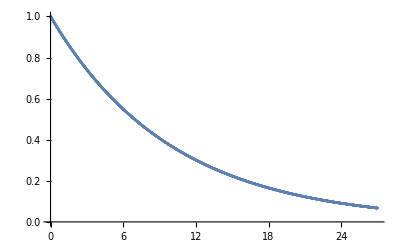

```mathematica
ListPlot[Transpose@{BinsOm, b[BinsOm, 0.1]}]
```

## Computation integrals for the evaluation of R,W

### Computation of R and Plot as a function of t

```mathematica
For[j=1, j<=NBins, j++, RMatrix[j] = Table[Integrate[b[K, j],{K, 0, Infinity}]]]
```

```mathematica
Table[RMatrix[i],{i,1,NBins}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22,1/23,1/24,1/25,1/26,1/27,1/28,1/29,1/30,1/31}

```mathematica
N[1/31,20]
```

0.032258064516129032258

```mathematica
RPlot = Table[RMatrix[i], {i,1,NBins}];
```

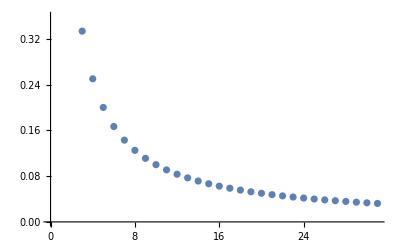

```mathematica
ListPlot[Transpose@{Binst, RPlot}]
```

```mathematica
Integrate[b[K,1]*b[K,1]*(K-1)^2, {K, 0, Infinity}]
```

1/4

### Computation of W and inversion

```mathematica
Clear[WMatrix]
```

```mathematica
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, WMatrix[i,j] = Table[Integrate[b[K,i]*b[K,j]*(K-BarOmega)^2,{K, 0, Infinity}]]]];
```

```mathematica
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++,WMatrixAn[i,j] = -(-2+2 BarOmega *(i+j)-BarOmega^2 (i+j)^2)/(i+j)^3]]
```

```mathematica
WMAN = Table[WMatrixAn[i,j],{i,1,NBins},{j,1,NBins}]
```

{{0.125,0.0462963,0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697},{0.0462963,0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314},{0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877},{0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318},{0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571},{0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578},{0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288},{0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651},{0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625},{0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317},{0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248},{0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828},{0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877},{0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368},{0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274},{0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572},{0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239},{0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255},{0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616},{0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257},{0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209},{0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442},{0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994},{0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269},{0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568},{0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898},{0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333},{0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975},{0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975,0.00389815},{0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975,0.00389815,0.00383843},{0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975,0.00389815,0.00383843,0.0037805}}

```mathematica
WM = Table[WMatrix[i,j],{i,1,NBins},{j,1,NBins}]
```

{{0.125,0.0462963,0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697},{0.0462963,0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314},{0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877},{0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318},{0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571},{0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578},{0.0195313,0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288},{0.0181756,0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651},{0.017,0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625},{0.0159654,0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317},{0.0150463,0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248},{0.0142239,0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828},{0.013484,0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877},{0.0128148,0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368},{0.012207,0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274},{0.0116528,0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572},{0.0111454,0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239},{0.0106794,0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255},{0.01025,0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616},{0.00985315,0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257},{0.00948535,0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209},{0.00914359,0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442},{0.00882523,0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994},{0.008528,0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269},{0.00824989,0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568},{0.00798913,0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898},{0.00774417,0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333},{0.00751363,0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975},{0.0072963,0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975,0.00389815},{0.00709107,0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975,0.00389815,0.00383843},{0.00689697,0.00671314,0.00653877,0.00637318,0.00621571,0.00606578,0.00592288,0.00578651,0.00565625,0.0055317,0.00541248,0.00529828,0.00518877,0.00508368,0.00498274,0.00488572,0.00479239,0.00470255,0.004616,0.00453257,0.00445209,0.00437442,0.0042994,0.0042269,0.0041568,0.00408898,0.00402333,0.00395975,0.00389815,0.00383843,0.0037805}}

```mathematica
N[5/216,25]
```

0.02314814814814814814814815

```mathematica
Rationalize[WM]
```

{{1/8,5/108,1/32,13/500,5/216,29/1372,5/256,53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384},{5/108,1/32,13/500,5/216,29/1372,5/256,53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748},{1/32,13/500,5/216,29/1372,5/256,53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304},{13/500,5/216,29/1372,5/256,53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500},{5/216,29/1372,5/256,53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328},{29/1372,5/256,53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612},{5/256,53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872},{53/2916,17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276},{17/1000,85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000},{85/5324,13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684},{13/864,125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088},{125/8788,37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028},{37/2744,173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592},{173/13500,25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500},{25/2048,229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336},{229/19652,65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292},{65/5832,293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296},{293/27436,41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596},{41/4000,365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000},{365/37044,101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604},{101/10648,445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304},{445/48668,61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508},{61/6912,533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464},{533/62500,145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500},{145/17576,629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500,365/87808},{629/78732,85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500,365/87808,3029/740772},{85/10976,733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500,365/87808,3029/740772,785/195112},{733/97556,197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500,365/87808,3029/740772,785/195112,3253/821516},{197/27000,845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500,365/87808,3029/740772,785/195112,3253/821516,421/108000},{845/119164,113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500,365/87808,3029/740772,785/195112,3253/821516,421/108000,3485/907924},{113/16384,965/143748,257/39304,1093/171500,145/23328,1229/202612,325/54872,1373/237276,181/32000,1525/275684,401/74088,1685/318028,221/42592,1853/364500,485/97336,2029/415292,265/55296,2213/470596,577/125000,2405/530604,313/70304,2605/595508,677/157464,2813/665500,365/87808,3029/740772,785/195112,3253/821516,421/108000,3485/907924,901/238328}}

```mathematica
Dimensions[WM]
```

{31,31}

```mathematica
WMM1 = Inverse[WM]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.125,0.0462963,0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,«21»},{0.0462963,0.03125,0.026,0.0231481,0.021137,0.0195313,0.0181756,0.017,0.0159654,0.0150463,«21»},«8»,«21»} may contain significant numerical errors.

{{1257.09,-86887.2,1.98265×10^6,-2.07453×10^7,1.0895×10^8,-2.57758×10^8,-1.22439×10^7,1.3351×10^9,-2.1563×10^9,-3.55561×10^8,3.02913×10^9,-1.04794×10^9,3.58346×10^8,-3.08693×10^9,2.0379×10^9,-3.07685×10^9,4.90237×10^9,2.15046×10^9,-2.81883×10^9,-1.56124×10^9,-2.76958×10^9,2.46768×10^9,-1.57385×10^9,4.06138×10^9,-6.23303×10^8,8.18662×10^8,1.29514×10^9,-5.76259×10^9,-2.65212×10^9,8.62889×10^9,-3.42006×10^9},{-88533.6,7.29409×10^6,-1.81337×10^8,1.99238×10^9,-1.07399×10^10,2.52205×10^10,6.68305×10^9,-1.54586×10^11,2.40807×10^11,7.16617×10^10,-4.29404×10^11,2.12682×10^11,-4.81899×10^10,3.11297×10^11,-2.61253×10^11,4.30134×10^11,-6.38845×10^11,-1.83169×10^11,3.66242×10^11,4.8498×10^10,3.83972×10^11,-2.65116×10^11,1.06022×10^11,-3.25246×10^11,-5.701×10^10,-7.09347×10^10,-1.05955×10^11,6.60038×10^11,2.52469×10^11,-9.50227×10^11,3.8313×10^11},{2.10605×10^6,-1.89285×10^8,4.96356×10^9,-5.63885×10^10,3.09099×10^11,-7.12447×10^11,-3.86789×10^11,5.19372×10^12,-7.75242×10^12,-3.65026×10^12,1.75905×10^13,-1.0837×10^13,2.032×10^12,-8.76966×10^12,9.96644×10^12,-1.76267×10^13,2.43684×10^13,3.49809×10^12,-1.38566×10^13,3.8005×10^12,-1.54655×10^13,8.04234×10^12,-6.69679×10^11,5.22855×10^12,7.05431×10^12,1.40301×10^12,1.9472×10^12,-2.19563×10^13,-6.25481×10^12,2.98595×10^13,-1.23039×10^13},{-2.3881×10^7,2.26325×10^9,-6.15542×10^10,7.16396×10^11,-3.96959×10^12,8.90374×10^12,7.84003×10^12,-7.71361×10^13,1.09445×10^14,7.76723×10^13,-3.2064×10^14,2.29726×10^14,-4.05171×10^13,1.03946×10^14,-1.74541×10^14,3.24249×10^14,-4.16907×10^14,-3.78744×10^12,2.35018×10^14,-1.579×10^14,2.7745×10^14,-1.03573×10^14,-3.98294×10^13,2.36457×10^13,-1.98345×10^14,-1.27925×10^12,-3.55971×10^12,3.24799×10^14,5.25388×10^13,-4.06254×10^14,1.72347×10^14},{1.47237×10^8,-1.44901×10^10,4.05388×10^11,-4.81396×10^12,2.69344×10^13,-5.89013×10^13,-7.17354×10^13,5.90892×10^14,-7.87141×10^14,-8.49674×10^14,3.10112×10^15,-2.48991×10^15,4.48916×10^14,-5.9597×10^14,1.6787×10^15,-3.17773×10^15,3.79167×10^15,-4.51536×10^14,-2.1327×10^15,2.27266×10^15,-2.63111×10^15,6.39157×10^14,7.84024×10^14,-1.18396×10^15,2.4859×10^15,-2.26911×10^14,-1.73103×10^14,-2.52275×10^15,-4.00647×10^12,2.76803×10^15,-1.22645×10^15},{-5.1583×10^8,5.24651×10^10,-1.50926×10^12,1.83578×10^13,-1.04902×10^14,2.33606×10^14,2.89753×10^14,-2.38859×10^15,2.90456×10^15,5.28771×10^15,-1.7244×10^16,1.51895×10^16,-2.98257×10^15,1.70298×10^15,-9.65193×10^15,1.78657×10^16,-1.96684×10^16,4.84655×10^15,1.12645×10^16,-1.64114×10^16,1.41874×10^16,-1.69717×10^15,-6.19251×10^15,1.12251×10^16,-1.667×10^16,2.89926×10^15,1.53247×10^15,1.09077×10^16,-2.4558×10^15,-9.41445×10^15,4.52806×10^15},{1.00399×10^9,-1.06645×10^11,3.20675×10^12,-4.10372×10^13,2.52342×10^14,-6.77081×10^14,-5.03108×10^13,4.03307×10^15,-3.83883×10^15,-1.96207×10^16,5.63546×10^16,-5.38892×10^16,1.2263×10^16,-2.65778×10^15,3.40439×10^16,-5.80065×10^16,5.80972×10^16,-2.24888×10^16,-3.58503×10^16,6.57105×10^16,-4.37489×10^16,-5.97597×10^14,2.59707×10^16,-5.17223×10^16,6.43665×10^16,-1.77409×10^16,-4.51953×10^15,-2.50148×10^16,1.58592×10^16,1.0416×10^16,-6.90572×10^15},{-1.00092×10^9,1.18479×10^11,-4.02237×10^12,5.98624×10^13,-4.59402×10^14,1.92132×10^15,-4.28338×10^15,5.07731×10^15,-9.91271×10^15,4.41022×10^16,-1.04322×10^17,1.08399×10^17,-3.10803×10^16,5.50104×10^15,-7.02932×10^16,9.8469×10^16,-8.62167×10^16,5.17457×10^16,6.91389×10^16,-1.46709×10^17,7.05351×10^16,1.49657×10^16,-6.40619×10^16,1.3438×10^17,-1.47227×10^17,6.34142×10^16,1.25786×10^15,1.85074×10^16,-4.70671×10^16,3.09419×10^16,-6.77954×10^15},{7.40947×10^8,-1.12799×10^11,4.84551×10^12,-9.14322×10^13,9.11006×10^14,-5.24052×10^15,1.80999×10^16,-3.80111×10^16,5.11247×10^16,-6.14984×10^16,9.60796×10^16,-1.11323×10^17,4.65845×10^16,-1.38855×10^16,6.36819×10^16,-4.248×10^16,2.20945×10^16,-4.9381×10^16,-8.31185×10^16,1.68601×10^17,-3.79195×10^16,-3.61256×10^16,1.08409×10^17,-2.20904×10^17,2.08696×10^17,-1.35463×10^17,1.09714×10^16,4.60912×10^16,7.75014×10^16,-1.27606×10^17,4.41949×10^16},{-1.76732×10^9,2.41579×10^11,-9.71837×10^12,1.76876×10^14,-1.73855×10^15,1.00524×10^16,-3.54101×10^16,7.56019×10^16,-9.32885×10^16,6.35083×10^16,-4.21324×10^16,5.86837×10^16,-3.95123×10^16,-6.82825×10^15,4.44783×10^16,-1.13043×10^17,8.86961×10^16,-3.70748×10^15,8.00325×10^16,-9.15972×10^16,-1.82326×10^16,3.68356×10^16,-1.73584×10^17,3.06156×10^17,-2.32562×10^17,1.51963×10^17,2.79969×10^16,-1.29045×10^17,-8.70735×10^16,1.92879×10^17,-6.92953×10^16},{2.8005×10^9,-3.52454×10^11,1.30671×10^13,-2.19699×10^14,2.00048×10^15,-1.07447×10^16,3.52646×10^16,-7.06493×10^16,8.48749×10^16,-6.99432×10^16,7.963×10^16,-1.02086×10^17,2.87647×10^16,1.04745×10^17,-1.59672×10^17,1.26506×10^17,-3.61587×10^16,-3.01572×10^15,-8.37511×10^16,1.01486×10^17,-4.32221×10^16,-2.37155×10^16,2.62607×10^17,-4.31972×10^17,2.74889×10^17,-2.25213×10^16,-1.55509×10^17,1.19647×10^17,9.17042×10^16,-1.46244×10^17,4.72926×10^16},{-1.02224×10^9,1.47053×10^11,-6.05994×10^12,1.1053×10^14,-1.06632×10^15,5.90775×10^15,-1.93198×10^16,3.69966×10^16,-4.42087×10^16,6.37276×10^16,-1.48004×10^17,1.98731×10^17,-3.35604×10^16,-1.68431×10^17,1.02353×10^17,4.68173×10^16,-8.81741×10^16,1.02251×10^17,3.18835×10^16,-1.93697×10^17,1.06007×10^17,4.25495×10^16,-2.11398×10^17,3.68283×10^17,-1.8183×10^17,-1.29877×10^17,1.66261×10^17,-3.85991×10^16,-5.50252×10^16,6.05703×10^16,-1.9253×10^16},{4.20528×10^8,-8.3955×10^10,4.29863×10^12,-9.22114×10^13,1.01476×10^15,-6.30426×10^15,2.29024×10^16,-4.79018×10^16,5.43443×10^16,-3.98554×10^16,6.3598×10^16,-8.7852×10^16,-1.60555×10^16,9.18162×10^16,2.52101×10^16,-4.86546×10^16,-6.3948×10^15,-1.0545×10^17,5.43355×10^16,8.30366×10^16,4.64187×10^16,-7.95378×10^16,1.16456×10^16,-2.68233×10^16,-6.78572×10^16,7.75216×10^16,-4.6199×10^14,3.84563×10^16,-5.79504×10^15,-6.23249×10^16,3.10563×10^16},{-2.34766×10^9,3.04082×10^11,-1.16333×10^13,2.02517×10^14,-1.91852×10^15,1.07984×10^16,-3.75357×10^16,8.06029×10^16,-1.01837×10^17,6.29579×10^16,6.49307×10^15,-6.2681×10^16,9.50449×10^16,-5.19036×10^16,-2.20671×10^16,-2.29135×10^16,6.39214×10^16,4.2238×10^15,8.41721×10^15,-2.61271×10^15,-1.1107×10^17,7.31821×10^16,3.79739×10^16,-4.75853×10^16,3.48605×10^16,-3.35867×10^16,7.21274×10^16,-5.16004×10^16,-7.99949×10^16,1.1382×10^17,-3.73072×10^16},{-1.28315×10^9,1.34161×10^11,-3.78236×10^12,3.97871×10^13,-9.96248×10^13,-1.20643×10^15,1.10126×10^16,-3.78379×10^16,5.14032×10^16,3.11447×10^16,-1.83361×10^17,1.77089×10^17,2.21092×10^16,-1.17955×10^17,1.03119×10^17,-1.10943×10^17,-5.25606×10^16,1.76307×10^17,2.03878×10^16,-1.11898×10^17,4.85701×10^16,4.29612×10^16,-3.29951×10^17,4.13818×10^17,-3.10628×10^17,3.40097×10^17,-1.0006×10^17,-1.44388×10^17,-6.11019×10^16,1.96371×10^17,-7.24365×10^16},{4.69195×10^9,-5.71095×10^11,1.99528×10^13,-3.0583×10^14,2.42152×10^15,-1.05133×10^16,2.50098×10^16,-3.59052×10^16,8.1769×10^16,-3.05448×10^17,6.34589×10^17,-4.96602×10^17,-2.17664×10^17,5.47387×10^17,-2.41046×10^17,-1.64661×10^16,3.63874×10^17,-4.57638×10^17,-3.40045×10^17,7.27269×10^17,-2.44916×10^17,-2.11081×10^17,9.27777×10^17,-1.51466×10^18,1.24938×10^18,-4.5878×10^17,-3.99038×10^17,2.66025×10^17,6.83117×10^17,-7.97188×10^17,2.38659×10^17},{9.44838×10^8,-7.86267×10^10,1.51027×10^12,-3.76531×10^12,-1.40519×10^14,1.57299×10^15,-7.80125×10^15,2.48686×10^16,-6.99526×10^16,1.84593×10^17,-3.37039×10^17,2.76457×10^17,9.0268×10^16,-2.39371×10^17,-6.29114×10^16,2.23789×10^17,-2.07217×10^17,2.14442×10^17,1.80778×10^17,-4.41186×10^17,6.83452×10^16,1.12661×10^17,-2.75177×10^17,7.16944×10^17,-5.7396×10^17,-1.35764×10^16,2.13309×10^17,1.15531×10^17,-5.10705×10^17,4.40114×10^17,-1.24632×10^17},{-5.78738×10^8,5.59381×10^10,-1.18617×10^12,6.60129×10^11,2.09303×10^14,-2.46788×10^15,1.25753×10^16,-2.88624×10^16,7.45308×10^14,1.55679×10^17,-3.61938×10^17,3.12614×10^17,6.72687×10^16,-3.81525×10^17,3.15971×10^17,6.59167×10^16,-4.18613×10^17,2.3704×10^17,3.38096×10^17,-5.79842×10^17,3.65216×10^17,8.35706×10^16,-6.17135×10^17,8.86951×10^17,-7.0357×10^17,8.60016×10^16,4.91093×10^17,-3.17626×10^17,-2.00253×10^17,2.67236×10^17,-7.43521×10^16},{-7.95182×10^9,1.03151×10^12,-3.89987×10^13,6.60815×10^14,-5.97735×10^15,3.12676×10^16,-9.69596×10^16,1.74726×10^17,-1.79138×10^17,1.62591×10^17,-2.90762×10^17,2.95263×10^17,1.51081×10^17,-4.02274×10^17,1.27962×10^17,-7.99233×10^16,-3.36962×10^16,4.07723×10^17,2.35478×10^16,-5.2305×10^17,1.80314×10^17,1.81775×10^17,-6.88711×10^17,1.22048×10^18,-1.03728×10^18,4.24376×10^17,2.60177×10^17,-2.31844×10^17,-5.54827×10^17,7.03652×10^17,-2.21111×10^17},{8.26698×10^9,-1.13874×10^12,4.53443×10^13,-8.0372×10^14,7.55979×10^15,-4.09159×10^16,1.31027×10^17,-2.47655×10^17,2.98419×10^17,-4.12691×10^17,8.10098×10^17,-8.23406×10^17,-2.5895×10^17,1.01691×10^18,-3.89797×10^17,-1.50054×10^17,5.41047×10^17,-8.76882×10^17,-4.9931×10^17,1.53576×10^18,-5.00976×10^17,-3.57118×10^17,1.4845×10^18,-2.82379×10^18,2.1542×10^18,-3.98603×10^17,-8.47182×10^17,4.92777×10^17,1.10241×10^18,-1.38561×10^18,4.38997×10^17},{-7.01482×10^9,9.09893×10^11,-3.44765×10^13,5.85883×10^14,-5.30724×10^15,2.76527×10^16,-8.41071×10^16,1.41549×10^17,-1.11112×10^17,5.26243×10^16,-1.72825×10^17,2.43832×10^17,1.30733×10^17,-4.0889×10^17,1.6961×10^17,-5.03457×10^16,-6.60266×10^16,2.76782×10^17,1.30483×10^17,-3.18202×10^17,-4.95227×10^16,9.10225×10^16,-5.1709×10^17,1.00416×10^18,-6.11357×10^17,1.98804×10^17,1.57623×10^17,-3.02767×10^17,-2.68923×10^17,5.31165×10^17,-1.90118×10^17},{9.307×10^9,-1.16351×10^12,4.2219×10^13,-6.81575×10^14,5.79596×10^15,-2.77768×10^16,7.45812×10^16,-1.00113×10^17,4.74675×10^16,-7.40467×10^16,3.54917×10^17,-3.93651×10^17,-2.24675×10^17,5.41798×10^17,-9.92173×10^16,-7.55606×10^16,1.49622×10^17,-4.22431×10^17,-2.35961×10^16,4.48411×10^17,-1.33285×10^17,-2.05163×10^17,7.69924×10^17,-1.19483×10^18,8.94097×10^17,-2.71769×10^17,-5.05887×10^17,4.46515×10^17,5.6098×10^17,-7.92623×10^17,2.51153×10^17},{-1.92601×10^9,2.72565×10^11,-1.09225×10^13,1.90726×10^14,-1.71752×10^15,8.47373×10^15,-2.224×10^16,2.53779×10^16,-7.81468×10^15,6.88782×10^16,-2.76042×10^17,2.78035×10^17,1.5301×10^17,-2.76753×10^17,-1.7958×10^17,2.72188×10^17,-2.02417×10^17,4.41722×10^17,-3.82383×10^14,-5.35679×10^17,7.30883×10^16,2.77777×10^17,-3.8469×10^17,7.46394×10^17,-5.31082×10^17,-2.06304×10^17,5.51795×10^17,-1.08783×10^17,-5.80739×10^17,5.91811×10^17,-1.74509×10^17},{-8.28745×10^9,1.07282×10^12,-4.03265×10^13,6.76249×10^14,-6.0182×10^15,3.07702×10^16,-9.31916×10^16,1.71905×10^17,-2.42669×10^17,4.68916×10^17,-9.1629×10^17,8.2209×10^17,3.07818×10^17,-1.0404×10^18,5.0626×10^17,3.34855×10^16,-4.23406×10^17,5.65339×10^17,6.15246×10^17,-1.40134×10^18,6.70492×10^17,1.86592×10^17,-1.48783×10^18,2.58229×10^18,-2.03015×10^18,6.11308×10^17,7.40227×10^17,-5.89088×10^17,-9.28571×10^17,1.23429×10^18,-3.88718×10^17},{4.17748×10^9,-5.5566×10^11,2.13562×10^13,-3.64706×10^14,3.29787×10^15,-1.71907×10^16,5.43518×10^16,-1.14748×10^17,2.19635×10^17,-4.85182×10^17,8.2761×10^17,-5.81923×10^17,-3.97382×10^17,7.981×10^17,-2.53764×10^17,-4.41415×10^16,3.23889×10^17,-4.67996×10^17,-6.5571×10^17,1.24365×10^18,-3.81178×10^17,-2.40131×10^17,1.2129×10^18,-2.19026×10^18,1.50363×10^18,-1.88418×10^17,-6.21266×10^17,3.29179×10^17,8.03755×10^17,-9.93431×10^17,3.13069×10^17},{3.59665×10^9,-4.69608×10^11,1.78496×10^13,-3.03026×10^14,2.72407×10^15,-1.38911×10^16,3.98492×10^16,-5.4952×10^16,3.39582×10^15,6.25172×10^16,3.28274×10^16,-1.83674×10^17,5.62597×10^16,1.24258×10^17,-1.30664×10^16,-3.32813×10^16,1.74122×10^16,-2.06229×10^17,1.00046×10^17,1.7141×10^17,-7.66219×10^16,2.10968×10^16,5.91476×10^13,-2.31147×10^17,2.99857×10^17,-1.13785×10^17,-1.35828×10^17,1.39667×10^17,1.47634×10^17,-2.35565×10^17,7.93115×10^16},{-5.04092×10^8,4.60445×10^10,-9.05651×10^11,-8.26212×10^11,1.75907×10^14,-1.93183×10^15,9.34983×10^15,-2.02791×10^16,6.48225×10^14,8.8919×10^16,-1.65242×10^17,7.24302×10^16,8.80262×10^16,-9.53726×10^16,7.42064×10^16,-8.12572×10^16,-6.71565×10^16,1.13277×10^17,3.66224×10^16,-6.05959×10^15,1.09632×10^16,-1.03004×10^17,-1.44501×10^17,3.3853×10^17,-1.98428×10^17,9.80275×10^16,1.60389×10^16,-1.52651×10^17,9.21121×10^16,9.80792×10^15,-1.32493×10^16},{-7.5087×10^8,1.00051×10^11,-4.0602×10^12,7.63227×10^13,-7.84369×10^14,4.72516×10^15,-1.66714×10^16,2.98689×10^16,-7.62107×10^13,-1.18819×10^17,2.45097×10^17,-1.92882×10^17,-3.80159×10^16,2.20687×10^17,-1.92076×10^17,-6.71654×10^16,3.27783×10^17,-2.37674×10^17,-2.1968×10^16,1.49838×10^17,-2.45174×10^17,4.93445×10^16,4.55383×10^17,-6.12936×10^17,4.51206×10^17,-1.82163×10^17,-2.38073×10^17,2.69492×10^17,1.14994×10^17,-2.24831×10^17,7.08175×10^16},{-5.87591×10^9,7.80944×10^11,-3.01491×10^13,5.19525×10^14,-4.75028×10^15,2.48486×10^16,-7.52781×10^16,1.2457×10^17,-9.68142×10^16,7.6119×10^16,-2.76858×10^17,4.05985×10^17,3.36454×10^16,-4.26595×10^17,1.36331×10^17,1.42331×10^17,-3.06648×10^17,4.79156×10^17,1.28405×10^17,-6.84438×10^17,3.01132×10^17,1.05849×10^17,-5.88075×10^17,1.08038×10^18,-8.31851×10^17,1.32262×10^17,5.21826×10^17,-2.88532×10^17,-6.91753×10^17,8.37311×10^17,-2.59049×10^17},{6.85764×10^9,-8.91587×10^11,3.38223×10^13,-5.74922×10^14,5.20506×10^15,-2.70645×10^16,8.17308×10^16,-1.33334×10^17,8.43482×10^16,1.64682×10^16,6.36019×10^16,-1.83252×10^17,-3.3008×10^16,1.92433×10^17,1.23112×10^16,-4.26564×10^15,1.43293×10^16,-2.55146×10^17,-1.07222×10^17,4.121×10^17,-3.04318×10^16,-6.91852×10^16,1.72274×10^17,-5.02467×10^17,3.48521×10^17,6.07179×10^15,-2.43359×10^17,8.2604×10^16,4.72404×10^17,-5.45692×10^17,1.70566×10^17},{-2.10705×10^9,2.69499×10^11,-1.007×10^13,1.68791×10^14,-1.50853×10^15,7.75126×10^15,-2.31315×10^16,3.69405×10^16,-1.97313×10^16,-2.01534×10^16,1.83666×10^16,1.0691×10^16,9.59995×10^15,-1.20003×10^16,-2.3909×10^16,-2.59953×10^16,4.01898×10^16,3.36359×10^16,2.41796×10^16,-5.66716×10^16,-3.66019×10^16,6.6295×10^15,1.82389×10^16,4.02632×10^16,-1.15437×10^16,-1.99321×10^16,1.91211×10^16,6.75837×10^15,-8.82329×10^16,9.77499×10^16,-3.08629×10^16}}

```mathematica
N[WMM1,30];
```

## Computation of the coefficients g_t

```mathematica
For[j=1, j<=NBins, j++,NVector[j]=0]
```

```mathematica
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, NVector[j] = NVector[j] +RMatrix[i]*WMM1[[j,i]]]; Print[N[NVector[j]]]]
```

-24.3126

3642.44

-126578.

1.87201×10^6

-1.39881×10^7

5.52597×10^7

-1.0424×10^8

2.5565×10^7

2.23508×10^8

-3.02813×10^8

1.13862×10^8

-1.88786×10^8

3.70606×10^8

-1.46493×10^8

-6.67363×10^7

3.33832×10^8

-4.59361×10^8

5.2917×10^7

-7.46305×10^8

1.62068×10^9

-7.91452×10^8

6.57255×10^8

-5.63878×10^8

-1.04762×10^9

8.72249×10^8

3.61769×10^8

1.57975×10^7

-8.85632×10^6

-7.88848×10^8

6.93879×10^8

-1.6955×10^8

```mathematica
DScal = 0
```

0

```mathematica
For[j=1, j<=NBins, j++,For[i=1,i<=NBins,i++, DScal = DScal +(RMatrix[j]*RMatrix[i])*WMM1[[j,i]]]]
```

```mathematica
Print[DScal]
```

64.8672

```mathematica
Clear[qFin]
```

```mathematica
For[j=1, j<=NBins, j++, qFin[j] = NVector[j]/DScal]
```

### Plot of g_t as a function of the bins of t

```mathematica
qPlot = Table[qFin[j], {j,1,NBins}];
```

```mathematica
Print[N[qPlot,10]]
```

{-0.374805,56.1523,-1951.34,28859.1,-215642.,851891.,-1.60698×10^6,394113.,3.44563×10^6,-4.6682×10^6,1.7553×10^6,-2.91035×10^6,5.71331×10^6,-2.25836×10^6,-1.02881×10^6,5.1464×10^6,-7.08157×10^6,815774.,-1.15051×10^7,2.49846×10^7,-1.22011×10^7,1.01323×10^7,-8.6928×10^6,-1.61502×10^7,1.34467×10^7,5.57707×10^6,243536.,-136530.,-1.2161×10^7,1.06969×10^7,-2.61381×10^6}

```mathematica
N[qFin[19],10] - N[qFin[20],10]
```

-3.64897×10^7

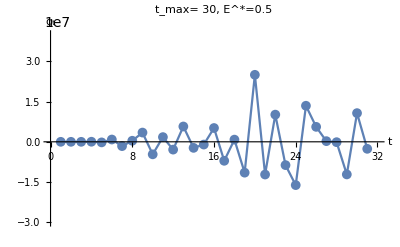

```mathematica
qOutPlot = ListLinePlot[Transpose@{Binst, qPlot}, PlotRange->{{0,32},{-3*^7,+4*^7}}, PlotMarkers->{Automatic, 10}, AxesLabel->{t,Subscript[g, t]},  PlotLabel->"t_max= 30,  E^*=0.5"]
```

```mathematica
Export["/Users/manuel/Documents/GitHub/Conducibility/Programmi/Coefficients.pdf",qOutPlot]
```

/Users/manuel/Documents/GitHub/Conducibility/Programmi/Coefficients.pdf

```mathematica
Clear[qFin]
```

```mathematica
qFin = Table[Get["/Users/manuel/Desktop/coeff.txt"]]
```

{-0.046305534046064865944800567215744995773018258975790460485592914561630750533446277333899816491688376383789758767119129985776847313733690467407516027259481447,25.585392501223555052428202900642288112073712860331979009283908542367123190324480507628092331314970173012738286668671793507650762786062410003378589538301802,-4673.3761209436279615220020896109472193480199817455437420937378106397471725030415805262181690958993446720917772090732816693570895846471013873251367828674276,422268.63900030362634795122739106660615041854077246771643470587948504177625232790634159519536724675610100351680401754276613231061515091759226557753939469301,-2.2591653706477367507963669966159397201120654535744756352950894346159633872930788029170257580597238189875777976444156286762785382626367149058732787384509618×10^7,7.9305576415727449335659755029145219269712427759464502763934878042993156809012405145846240118423451358297298189950052649072276776988676184762453076886651694×10^8,-1.9515351197143166733057353270054771011455138905057483948027361779589445658247864947797527947326035622510785260787262335763877973778969277991105439481652772×10^10,3.5237708527713339717335524028169425252564371402808659186473001088682220699798658993901642660071618007189185691344059026230533111227361521352642068009820232×10^11,-4.8251010513476308801562868416375329776667490702448506719743333865182529013778413526521222874267270010132673374766314272707407002855907468122576897440955295×10^12,5.1337735910895101307381317085558748519162374237806267613039934451501060764838921197555337215132819673500711597201155241263718113376057117372659516951032002×10^13,-4.3214851248714911666983652223274802758287756486242205735130525053270304805324892504928385912178361453108922237413054974149321960104920639562007541102060004×10^14,2.9159124452447196387043656354608370276747088588755919793578864445415053487596322507438572885753843720389231410158623918221078522150229902339124177317398981×10^15,-1.5909493109165583090058755050693249611594027228167570808341988157152919284247377247065019671794182943238977990069392248516422793070083384899649379475362502×10^16,7.0498542903944622376211259440639122879520154516457555803527346631520519868087990676929251502168275628840938946094134319983524984434836434639226788711990149×10^16,-2.5348448592789563165292882783982712977386503290380922390262040194341298270956625059517717763296395890674673734129766064678237737789491371604995047949881512×10^17,7.329565950246283990362658530480744703230966290873093792378842121292035969773977562638848321475959575436948109422254425141876604212451001574029031029940185×10^17,-1.6625212317842541384506716929507117213005747035823630334300174283665869725566349157589011558239946586330720512400254800255057854680158588894799924206034305×10^18,2.7637164418261719745197040152888875273322162396862383627400298927406144698454852932715215921542494774636842546682555603688956824704683522652295856448695597×10^18,-2.5672726088084680345151927944919153406267836314430804132895138580241984821073921132952543974208842847489310507604118069459567701426979944740802846231542803×10^18,-2.0136698566939585385669146629333499595083563916758932631000119850849041942825185288401810049210792185780468463124145851409198001741359459223866191054918674×10^18,1.4435969404990299288525224891292585129143914872236179379762896577668333483935349657847935414876190844708304569238574926878173261503345106666516362433588999×10^19,-3.513632386415492495998741469418474720510508193543973782136797375348496121465951183980993168364682692875128349456881591092965251622034151533231818416247817×10^19,5.8431408626937338601015332612880338085358220621175910281846555423298880761138782975952339213748967590743579721669212197364015647510910497053125650096233842×10^19,-7.3969784056403277922663852206844625851397593250068568166916245992234893687359889060465963691001879528682633795329723529544379870735231541474179171268564118×10^19,7.3600081087871666329936079011588168430289324583786279684212681945218054383470340995331116899034337525141950997790281077941971769847592422318985958014491598×10^19,-5.795494922725268027861209393000797633250249381462418899664643796599219090799247552413584762579645747075694511952553977107019102389456392745804803530805179×10^19,3.5865064703960350899022974359037083100452153619855941936224999340394882711713698882524892499677787901146541065557252883025635081493301939330491929604711124×10^19,-1.7116378555407580171120061943323448355160696649230865457528663714135218782214163363670003879791677287750696139899542764941284231244317254226861818861173101×10^19,6.0888954346863765053577444825324481224774560023930759020548640498444156981795511501771295797087066461739698446606781872913025403301202774762551291454009796×10^18,-1.5216768199394795940809912553025987505515420827424304314193551795717480920242609295506630817966369724960452966835761247785157398879467441215332466983329435×10^18,2.3849403253216361739527570786924913052262824390902142780929796591527026090361276097658841093064890958311954311537354624443300361912314356119900201553059365×10^17,-1.7645281451493400254204153486436437274590818047532205460392622635949187629724132438405008473549498080461003572310535557077596489817511456033880722818651778×10^16}

```mathematica
Dimensions[qFin]
```

{32}

## Computation of the smearing function Delta and plot

```mathematica
DeltaBar[Om_] = Sum[qFin[[i]]*b[Om,i],{i,32}]
```

-1.7645281451493400254204153486436437274590818047532205460392622635949187629724132438405008473549498080461003572310535557077596489817511456033880722818651778×10^16 ⅇ^(-32 Om)+2.3849403253216361739527570786924913052262824390902142780929796591527026090361276097658841093064890958311954311537354624443300361912314356119900201553059365×10^17 ⅇ^(-31 Om)-1.5216768199394795940809912553025987505515420827424304314193551795717480920242609295506630817966369724960452966835761247785157398879467441215332466983329435×10^18 ⅇ^(-30 Om)+6.0888954346863765053577444825324481224774560023930759020548640498444156981795511501771295797087066461739698446606781872913025403301202774762551291454009796×10^18 ⅇ^(-29 Om)-1.7116378555407580171120061943323448355160696649230865457528663714135218782214163363670003879791677287750696139899542764941284231244317254226861818861173101×10^19 ⅇ^(-28 Om)+3.5865064703960350899022974359037083100452153619855941936224999340394882711713698882524892499677787901146541065557252883025635081493301939330491929604711124×10^19 ⅇ^(-27 Om)-5.795494922725268027861209393000797633250249381462418899664643796599219090799247552413584762579645747075694511952553977107019102389456392745804803530805179×10^19 ⅇ^(-26 Om)+7.3600081087871666329936079011588168430289324583786279684212681945218054383470340995331116899034337525141950997790281077941971769847592422318985958014491598×10^19 ⅇ^(-25 Om)-7.3969784056403277922663852206844625851397593250068568166916245992234893687359889060465963691001879528682633795329723529544379870735231541474179171268564118×10^19 ⅇ^(-24 Om)+5.8431408626937338601015332612880338085358220621175910281846555423298880761138782975952339213748967590743579721669212197364015647510910497053125650096233842×10^19 ⅇ^(-23 Om)-3.513632386415492495998741469418474720510508193543973782136797375348496121465951183980993168364682692875128349456881591092965251622034151533231818416247817×10^19 ⅇ^(-22 Om)+1.4435969404990299288525224891292585129143914872236179379762896577668333483935349657847935414876190844708304569238574926878173261503345106666516362433588999×10^19 ⅇ^(-21 Om)-2.0136698566939585385669146629333499595083563916758932631000119850849041942825185288401810049210792185780468463124145851409198001741359459223866191054918674×10^18 ⅇ^(-20 Om)-2.5672726088084680345151927944919153406267836314430804132895138580241984821073921132952543974208842847489310507604118069459567701426979944740802846231542803×10^18 ⅇ^(-19 Om)+2.7637164418261719745197040152888875273322162396862383627400298927406144698454852932715215921542494774636842546682555603688956824704683522652295856448695597×10^18 ⅇ^(-18 Om)-1.6625212317842541384506716929507117213005747035823630334300174283665869725566349157589011558239946586330720512400254800255057854680158588894799924206034305×10^18 ⅇ^(-17 Om)+7.329565950246283990362658530480744703230966290873093792378842121292035969773977562638848321475959575436948109422254425141876604212451001574029031029940185×10^17 ⅇ^(-16 Om)-2.5348448592789563165292882783982712977386503290380922390262040194341298270956625059517717763296395890674673734129766064678237737789491371604995047949881512×10^17 ⅇ^(-15 Om)+7.0498542903944622376211259440639122879520154516457555803527346631520519868087990676929251502168275628840938946094134319983524984434836434639226788711990149×10^16 ⅇ^(-14 Om)-1.5909493109165583090058755050693249611594027228167570808341988157152919284247377247065019671794182943238977990069392248516422793070083384899649379475362502×10^16 ⅇ^(-13 Om)+2.9159124452447196387043656354608370276747088588755919793578864445415053487596322507438572885753843720389231410158623918221078522150229902339124177317398981×10^15 ⅇ^(-12 Om)-4.3214851248714911666983652223274802758287756486242205735130525053270304805324892504928385912178361453108922237413054974149321960104920639562007541102060004×10^14 ⅇ^(-11 Om)+5.1337735910895101307381317085558748519162374237806267613039934451501060764838921197555337215132819673500711597201155241263718113376057117372659516951032002×10^13 ⅇ^(-10 Om)-4.8251010513476308801562868416375329776667490702448506719743333865182529013778413526521222874267270010132673374766314272707407002855907468122576897440955295×10^12 ⅇ^(-9 Om)+3.5237708527713339717335524028169425252564371402808659186473001088682220699798658993901642660071618007189185691344059026230533111227361521352642068009820232×10^11 ⅇ^(-8 Om)-1.9515351197143166733057353270054771011455138905057483948027361779589445658247864947797527947326035622510785260787262335763877973778969277991105439481652772×10^10 ⅇ^(-7 Om)+7.9305576415727449335659755029145219269712427759464502763934878042993156809012405145846240118423451358297298189950052649072276776988676184762453076886651694×10^8 ⅇ^(-6 Om)-2.2591653706477367507963669966159397201120654535744756352950894346159633872930788029170257580597238189875777976444156286762785382626367149058732787384509618×10^7 ⅇ^(-5 Om)+422268.63900030362634795122739106660615041854077246771643470587948504177625232790634159519536724675610100351680401754276613231061515091759226557753939469301 ⅇ^(-4 Om)-4673.3761209436279615220020896109472193480199817455437420937378106397471725030415805262181690958993446720917772090732816693570895846471013873251367828674276 ⅇ^(-3 Om)+25.585392501223555052428202900642288112073712860331979009283908542367123190324480507628092331314970173012738286668671793507650762786062410003378589538301802 ⅇ^(-2 Om)-0.046305534046064865944800567215744995773018258975790460485592914561630750533446277333899816491688376383789758767119129985776847313733690467407516027259481447 ⅇ^-Om

```mathematica
N[DeltaBar[0.5],10]
```

4.

### Plot of Delta as a function of the Energy

```mathematica
Binnaggio = Range[0.0, 1, 0.01];
```

```mathematica
Dimensions[Binnaggio]
```

{101}

```mathematica
AAA =Table[DeltaBar[Binnaggio]];
```

```mathematica
BBB = Table[Binnaggio];
```

```mathematica
sdata = Transpose@{BBB, AAA};
```

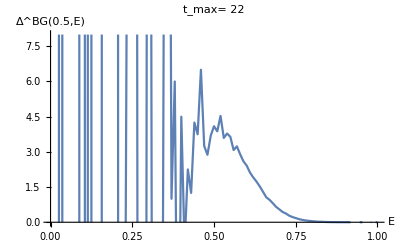

```mathematica
AAA =ListLinePlot[sdata, PlotRange->{{0,1},{0,8}}, AxesLabel->{"E","Δ^BG(0.5,E)"}, PlotLabel->"t_max= 22"]
```

### Output

```mathematica
Export["/Users/manuel/Documents/GitHub/Conducibility/Programmi/Delta_3.10.png",AAA]
```

Part::partd: Part specification $Failed⟦3,2⟧ is longer than depth of object.

Set::partd: Part specification System`ConvertersDump`evalOpts$4851704⟦3,2⟧ is longer than depth of object.

FilterRules::rep: $Failed is not a valid replacement rule.

/Users/manuel/Documents/GitHub/Conducibility/Programmi/Delta_3.10.png